Implementing kinematical cuts for the PANDA  p̄p→π^0γ^* →π^0l^+l^- by F.Maas et al.

```mathematica
(*Cosine of the s-channel c.m. frame scattering angle*)
Λ[X_,Y_,Z_]:=√(X^2+Y^2+Z^2-2*X*Y-2*X*Z-2*Y*Z)
(*COSΘ[S_,Q2_,T_]:=-(1/4( 2*M^2+m^2+Q2-S-2T))/(√(1/4 S-M^2)√(-1/2(Q2+m^2)+1/4 S+1/(4*S)(Q2-m^2)^2))*)
(*COSΘ[S_,Q2_,T_]:=-( 2*M^2+m^2+Q2-S-2T)/(Λ[S,M^2,M^2]/(√S) Λ[Q2,S,m^2]/(√S))*)
COSΘ[S_,Q2_,T_]:=-(1/2( 2*M^2+m^2+Q2-S-2T))/(√(1/4 S-M^2) Λ[Q2,S,m^2]/(√S))
```

```mathematica
(*Subscript[t, max] and Subscript[t, min] as the function of s and Q^2*)
Tmax[W2_,Q2_]:=1/2 (m^2+ √(W2-4 M^2) √((m^4-2 m^2 (Q2+W2)+(Q2-W2)^2)/W2)+2 M^2+Q2-W2)
Tmin[W2_,Q2_]:=1/2 (m^2- √(W2-4 M^2) √((m^4-2 m^2 (Q2+W2)+(Q2-W2)^2)/W2)+2 M^2+Q2-W2)
(*Subscript[t, cut] as the function of s, Q^2 and Subscript[Cosθ, cut]*)
Tcut[W2_,Q2_,CosCut_]:=1/2 (m^2+CosCut* √(W2-4 M^2) √((m^4-2 m^2 (Q2+W2)+(Q2-W2)^2)/W2)+2 M^2+Q2-W2)
(*|Subscript[p, π]^(->)|^2  in the c.m. frame as the function of s, Q^2*)
(*Note it is in 3D*) 
Ppi2[S_,Q2_]:=1/(4*S)(S^2-2(Q2+m^2)*S+(Q2-m^2)^2)
(*Note it is in Minkovsky*)
Δt2Exact[S_,Q2_,T_]:= -Ppi2[S,Q2]*(1-COSΘ[S,Q2,T]^2)
```

```mathematica
(*Approximate formulas from PRD 86*)
Δt2[XI_,DELTA2_]:=((1-XI) (DELTA2-2 XI (M^2/(1+XI)-m^2/(1-XI))))/(1+XI)
Δ2max[XI_]:=(2 XI (M^2 (-1+XI)+m^2 (1+XI)))/(-1+XI^2)
Δ2cut[XI_,ΔT2cut_]:=(2 XI (M^2 (-1+XI)+m^2 (1+XI)))/(-1+XI^2)+((1+XI) ΔT2cut)/(1-XI)
(*Expression fo ξ withot mass corrections*)
XII[WW2_,QQ2_]:=QQ2/(2*WW2-QQ2)
(*Expression fo ξ with mass corrections Eq. (A.18) PRD 86*)
XIICorrected[WW2_,QQ2_,T_]:=(QQ2-T-M^2)/(2*WW2-QQ2+T-3M^2)
```

```mathematica
(*On the Boost from CMS to LAB*)
```

```mathematica
Boost[p_,V_]:={(p[[1]]-V*p[[4]])/(√(1-V^2)),0,0,(p[[4]]-V*p[[1]])/(√(1-V^2))}
RelInt[p_]:=p[[1]]^2-p[[4]]^2
RelProd[p_,n_]:=p[[1]]*n[[1]]-p[[4]]*n[[4]]
```

```mathematica
M:=M
m:=m
W2:=W2
Q2:=Q2
(*Nucleon momentum in CMS*)
pN={(√W2)/2,0,0,-√(W2/4-M^2)};
(*Nucleon is on shell*) 
RelInt[pN]
(*Nucleon is at rest in LAB*) 
FullSimplify[Boost[pN,-(√(-4 M^2+W2))/(√W2)],Assumptions->{W2>0,W2>4M^2,M>0}]
```

M^2

{M,0,0,0}

```mathematica
(*pion longitudinal momentum in CMS*)
ppiCMS={√(m^2+Ppi2[W2,Q2]),0,0,√Ppi2[W2,Q2] COSΘ[W2,Q2,T]}

(*pion longitudinal momentim boosted to LAB*) 
Simplify[Boost[ppiCMS,-(√(-4 M^2+W2))/(√W2)],Assumptions->{W2>0,W2>4M^2,M>0}]
```

{√(m^2+((-m^2+Q2)^2-2 (m^2+Q2) W2+W2^2)/(4 W2)),0,0,-((m^2+2 M^2+Q2-2 T-W2) √W2 √(((-m^2+Q2)^2-2 (m^2+Q2) W2+W2^2)/W2))/(4 √(-M^2+W2/4) √(m^4-2 m^2 Q2+Q2^2-2 m^2 W2-2 Q2 W2+W2^2))}

{(-m^2-2 M^2-Q2+2 T+W2+√((m^2-Q2+W2)^2))/(4 M),0,0,(-m^2 W2+W2 (-Q2+2 T+W2+√((m^2-Q2+W2)^2))-2 M^2 (W2+2 √((m^2-Q2+W2)^2)))/(4 M √(W2 (-4 M^2+W2)))}

```mathematica
(*pion energy in the LAB frame*) 
EpiLab[W2_,Q2_,T_]:=(√((m^2-Q2+W2)^2)-m^2-2 M^2-Q2+2 T+W2)/(4 M)
```

Kinematical bin W^2=5 GeV^2,   3 GeV^2≤Q^2≤4.3 GeV^2

```mathematica
W2=5
Q2=3.8

CosCut=Cos[π/3]
```

5

3.8

1/2

For W^2= 5 Gev^2, Q^2= 3.8 Gev^2 and θ_cut= 60° t_cut= 0.435062 GeV^2

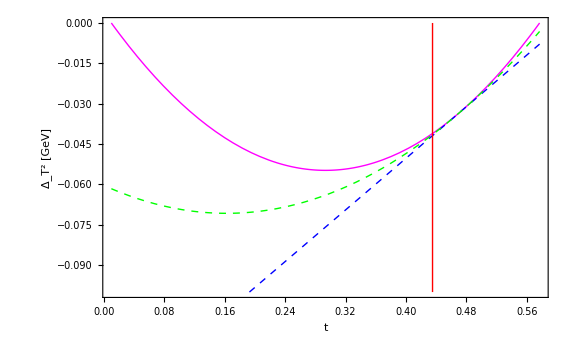

```mathematica
g1=Plot[Δt2Exact[W2,Q2,t],{t,Tmin[W2,Q2],Tmax[W2,Q2]},PlotRange->{0,-0.1},PlotStyle->{Magenta,Thick}]
g2=Plot[Δt2[XII[W2,Q2],t],{t,Tmin[W2,Q2],Tmax[W2,Q2]},PlotRange->{0,-0.1},PlotStyle->{Blue,Thick,Dashed}]
g3=Plot[Δt2[XIICorrected[W2,Q2,t],t],{t,Tmin[W2,Q2],Tmax[W2,Q2]},PlotRange->{0,-0.1},PlotStyle->{Green,Thick,Dashed}]

g4=ContourPlot[t==Tcut[W2,Q2,CosCut],{t,Tmin[W2,Q2],Tmax[W2,Q2]},{y,0,-0.1},ContourStyle->{Red,Thick}  ]

Print["For W^2= ",W2, " Gev^2, ","Q^2= ",Q2," Gev^2 and θ_cut= ",ArcCos[CosCut] 180/π,"°", " t_cut= ",Tcut[W2,Q2,CosCut]," GeV^2"]

Show[g1,g2,g3,g4,Frame->True,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"t"," Δ_T^2 [GeV]","W^2=5 GeV^2, Q^2=4 GeV^2",""}]
```

```mathematica
M:=0.940
m=0.140
```

0.14

5

1/2

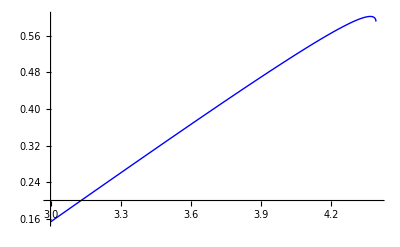

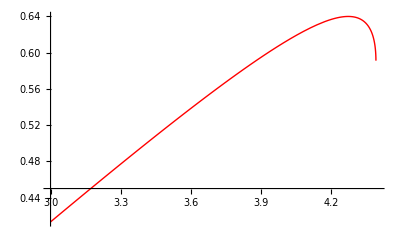

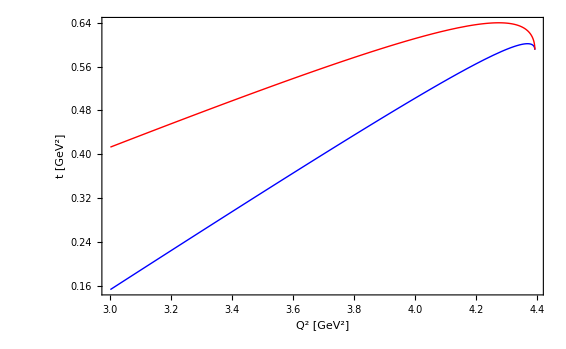

3

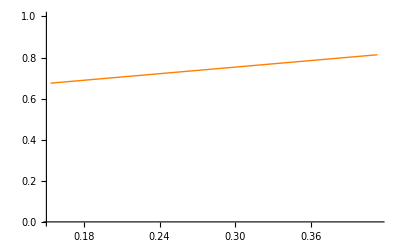

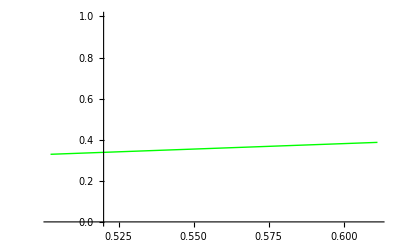

4.3

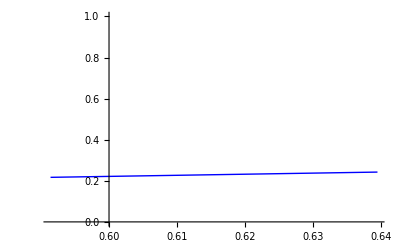

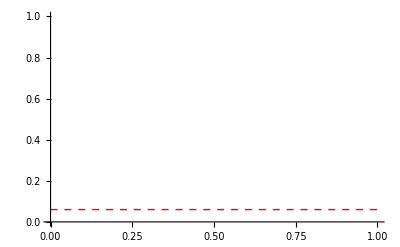

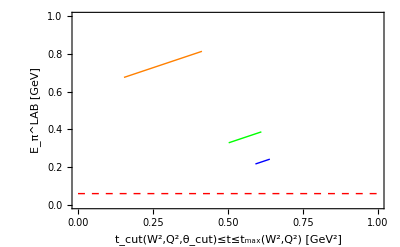

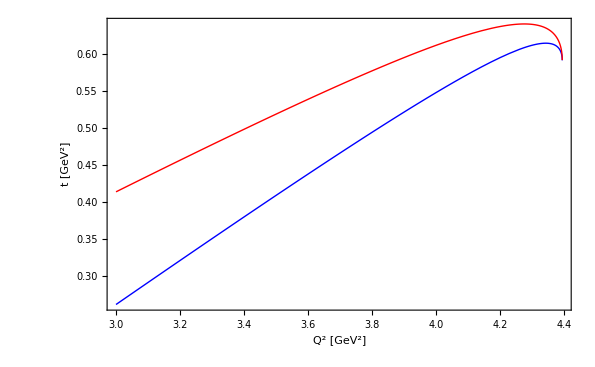

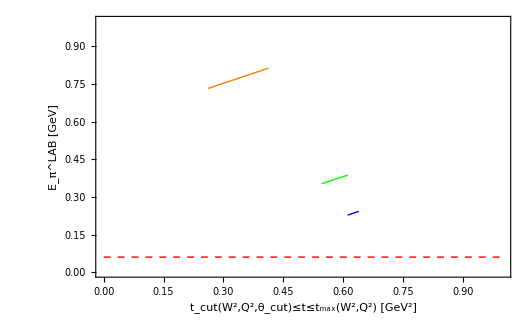

```mathematica
W2=5
CosCut=Cos[π/3]

r1=Plot[Tcut[W2,Q2,CosCut],{Q2,3,4.4},PlotStyle->Blue]
r2=Plot[Tmax[W2,Q2],{Q2,3,4.4},PlotStyle->Red]

Show[r1,r2,PlotRange->All,Frame->True,Axes->None,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Q^2 [GeV^2]"," t [GeV^2]","W^2=5 GeV^2 Cos θ_cut=1/2",""}]

Qmin=3

f1=Plot[EpiLab[W2,Qmin,t],{t,Tcut[W2,Qmin,CosCut],Tmax[W2,Qmin]},PlotRange->{0,1},PlotStyle->{Orange,Thick}]

f2=Plot[EpiLab[W2,4,t],{t,Tcut[W2,4,CosCut],Tmax[W2,4]},PlotRange->{0,1},PlotStyle->{Green,Thick}]


Qmax=4.30

f3=Plot[EpiLab[W2,Qmax,t],{t,Tcut[W2,Qmax,CosCut],Tmax[W2,Qmax]},PlotRange->{0,1},PlotStyle->{Blue,Thick}]

(*Subscript[E, π]^LAB≥ 2× 0.03 GeV*)
f0=Plot[0.06,{t,0,1},PlotStyle->{Red,Dashed},PlotRange->{0,1}]

Show[f0,f1,f2,f3,Frame->True,Axes->None,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"t_cut(W^2,Q^2,θ_cut)≤t≤t_max(W^2,Q^2) [GeV^2]"," E_π^LAB [GeV]","Q^2=3, 4, 4.3 GeV^2 Cos θ_cut=1/√2",""}]
```

Kinematical bin W^2=10 GeV^2, 5 GeV^2≤Q^2≤9 GeV^2

```mathematica
W2=10
Q2=7.5
CosCut=Cos[π/4]
```

10

7.5

1/(√2)

For W^2= 10 Gev^2, Q^2= 7.5 Gev^2 and θ_cut= 45°, t_cut= 0.314007 GeV^2, Δ_Tcut^2= -0.0695548 GeV^2

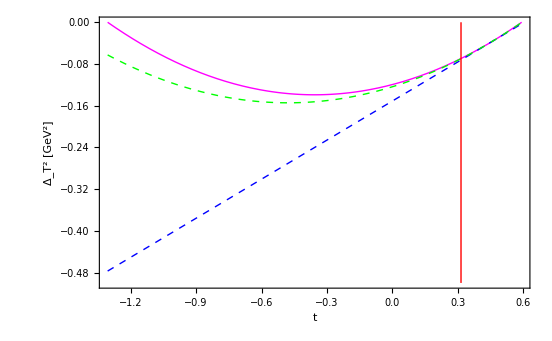

```mathematica
g1=Plot[Δt2Exact[W2,Q2,t],{t,Tmin[W2,Q2],Tmax[W2,Q2]},PlotRange->{0,-0.5},PlotStyle->{Magenta,Thick}]
g2=Plot[Δt2[XII[W2,Q2],t],{t,Tmin[W2,Q2],Tmax[W2,Q2]},PlotRange->{0,-0.5},PlotStyle->{Blue,Thick,Dashed}]
g3=Plot[Δt2[XIICorrected[W2,Q2,t],t],{t,Tmin[W2,Q2],Tmax[W2,Q2]},PlotRange->{0,-0.5},PlotStyle->{Green,Thick,Dashed}]

g4=ContourPlot[t==Tcut[W2,Q2,CosCut],{t,Tmin[W2,Q2],Tmax[W2,Q2]},{y,0,-0.5},ContourStyle->{Red,Thick} ]

Print["For W^2= ",W2, " Gev^2, ","Q^2= ",Q2," Gev^2 and θ_cut= ",ArcCos[CosCut] 180/π,"°,", " t_cut= ",Tcut[W2,Q2,CosCut]," GeV^2,", " Δ_Tcut^2= ",-Ppi2[W2,Q2](1-CosCut^2)," GeV^2"]

Show[g1,g2,g3,g4,Frame->True,Axes->None,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"t"," Δ_T^2 [GeV^2]","W^2=5 GeV^2, Q^2=7.5 GeV^2",""}]
```

10

1/(√2)

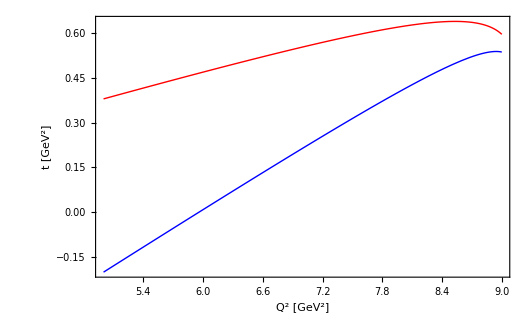

5

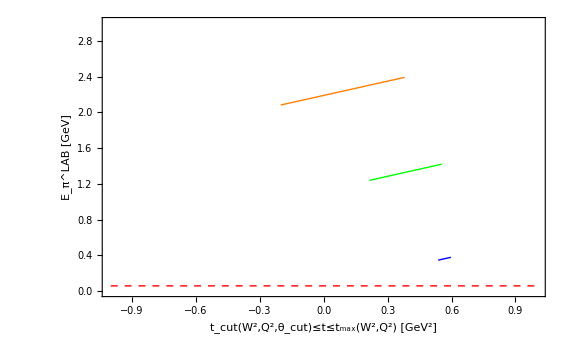

```mathematica
W2=10
CosCut=Cos[π/4]

r1=Plot[Tcut[W2,Q2,CosCut],{Q2,5,9},PlotStyle->Blue]
r2=Plot[Tmax[W2,Q2],{Q2,5,9},PlotStyle->Red]

Show[r1,r2,PlotRange->All,Frame->True,Axes->None,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Q^2 [GeV^2]"," t [GeV^2]","W^2=10 GeV^2 Cos θ_cut=1/√2",""}]

Qmin=5

f1=Plot[EpiLab[W2,Qmin,t],{t,Tcut[W2,Qmin,CosCut],Tmax[W2,Qmin]},PlotRange->All,PlotStyle->{Orange,Thick}]

f2=Plot[EpiLab[W2,7,t],{t,Tcut[W2,7,CosCut],Tmax[W2,7]},PlotRange->{0,3},PlotStyle->{Green,Thick}]


Qmax=9

f3=Plot[EpiLab[W2,Qmax,t],{t,Tcut[W2,Qmax,CosCut],Tmax[W2,Qmax]},PlotRange->{0,3},PlotStyle->{Blue,Thick}]

f0=Plot[0.06,{t,-1,1},PlotStyle->{Red,Dashed},PlotRange->{0,3}]

Show[f0,f1,f2,f3,Frame->True,Axes->None,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"t_cut(W^2,Q^2,θ_cut)≤t≤t_max(W^2,Q^2) [GeV^2]"," E_π^LAB [GeV]","Q^2=5, 7, 9 GeV^2 Cos θ_cut=1/√2",""}]
```

10

1/2

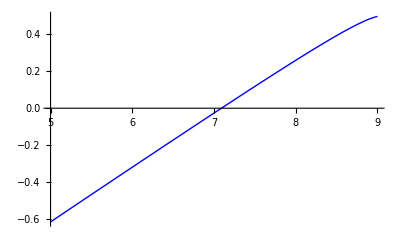

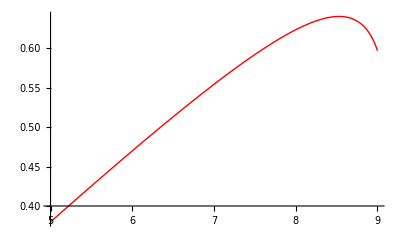

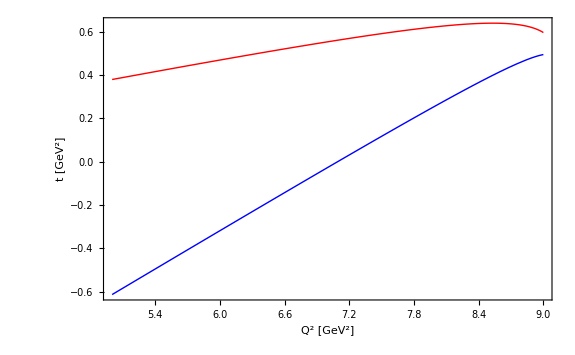

```mathematica
W2=10
CosCut=Cos[π/3]

r1=Plot[Tcut[W2,Q2,CosCut],{Q2,5,9},PlotStyle->Blue]
r2=Plot[Tmax[W2,Q2],{Q2,5,9},PlotStyle->Red]

Show[r1,r2,PlotRange->All,Frame->True,Axes->None,FrameStyle->Directive[FontSize->25,FontFamily->"TimesNewRoman"],FrameLabel->{"Q^2 [GeV^2]"," t [GeV^2]","W^2=10 GeV^2 Cos θ_cut=1/2",""}]
```